COMPETITION

Probability l<c

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability c<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)/2
```

Probability l=L

```mathematica
P3[L_,p_]:=p^L/2
```

```mathematica
S1[c_,p_]:=Sum[P1[l,p]*Log[2,P1[l,p]],{l,0,c-1}]
```

```mathematica
S2[L_,c_,p_]:=Sum[P2[l,p]*Log[2,P2[l,p]],{l,c,L-1}]
ENC[L_,c_,p_]:= -(S1[c,p]+2*S2[L,c,p]+2*P3[L,p]*Log[2,P3[L,p]])
```

ORDERED

P(l<L)

```mathematica
P1[l_,p_]:=(1-p)* p^l
```

P(l=L)

```mathematica
P2[L_,p_]:=p^L
```

```mathematica
ENO[L_,p_]:=-(Sum[P1[l,p]*Log[2,P1[l,p]],{l,0,L-1}]+p^L*Log[2,p^L])
```

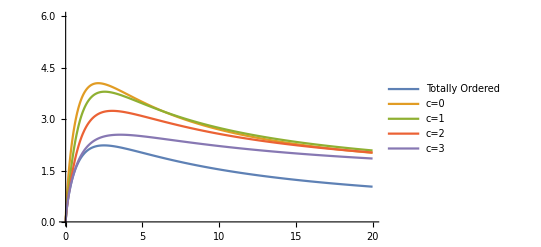

```mathematica
Plot[{ENO[4,1/(1+1/x)],ENC[4,1,1/(1+1/x)],ENC[4,2,1/(1+1/x)],ENC[4,3,1/(1+1/x)], ENC[4,4,1/(1+1/x)]},{x,0,20},PlotRange->{0,6}, PlotLegends->{"Totally Ordered","c=0","c=1","c=2","c=3"}]
```